```mathematica
SetDirectory[NotebookDirectory[]];
```

## T_scaling

```mathematica
fpi=Flatten[Import["./mub0/buffer/fpi.dat"]];
T=Flatten[Import["./mub0/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub10/buffer/fpi.dat"]];
T=Flatten[Import["./mub10/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub10=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub54/buffer/fpi.dat"]];
T=Flatten[Import["./mub54/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub54=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub55/buffer/fpi.dat"]];
T=Flatten[Import["./mub55/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub55=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub56/buffer/fpi.dat"]];
T=Flatten[Import["./mub56/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub56=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub60/buffer/fpi.dat"]];
T=Flatten[Import["./mub60/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub60=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub100/buffer/fpi.dat"]];
T=Flatten[Import["./mub100/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub100=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub104/buffer/fpi.dat"]];
T=Flatten[Import["./mub104/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub104=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub105/buffer/fpi.dat"]];
T=Flatten[Import["./mub105/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub105=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub106/buffer/fpi.dat"]];
T=Flatten[Import["./mub106/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub106=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub110/buffer/fpi.dat"]];
T=Flatten[Import["./mub110/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub110=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub200/buffer/fpi.dat"]];
T=Flatten[Import["./mub200/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub200=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub204/buffer/fpi.dat"]];
T=Flatten[Import["./mub204/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub204=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub205/buffer/fpi.dat"]];
T=Flatten[Import["./mub205/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub205=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub206/buffer/fpi.dat"]];
T=Flatten[Import["./mub206/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub206=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub304/buffer/fpi.dat"]];
T=Flatten[Import["./mub304/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub304=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub305/buffer/fpi.dat"]];
T=Flatten[Import["./mub305/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub305=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub306/buffer/fpi.dat"]];
T=Flatten[Import["./mub306/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub306=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub210/buffer/fpi.dat"]];
T=Flatten[Import["./mub210/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub210=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub300/buffer/fpi.dat"]];
T=Flatten[Import["./mub300/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub310/buffer/fpi.dat"]];
T=Flatten[Import["./mub310/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub310=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub400/buffer/fpi.dat"]];
T=Flatten[Import["./mub400/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub404/buffer/fpi.dat"]];
T=Flatten[Import["./mub404/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub404=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub405/buffer/fpi.dat"]];
T=Flatten[Import["./mub405/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub405=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub406/buffer/fpi.dat"]];
T=Flatten[Import["./mub406/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub406=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub410/buffer/fpi.dat"]];
T=Flatten[Import["./mub410/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub410=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub600/buffer/fpi.dat"]];
T=Flatten[Import["./mub600/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub604/buffer/fpi.dat"]];
T=Flatten[Import["./mub604/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub604=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub605/buffer/fpi.dat"]];
T=Flatten[Import["./mub605/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub605=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub606/buffer/fpi.dat"]];
T=Flatten[Import["./mub606/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub606=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub699p5/buffer/fpi.dat"]];
T=Flatten[Import["./mub699p5/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub699p5=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub700/buffer/fpi.dat"]];
T=Flatten[Import["./mub700/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
fpi=Flatten[Import["./mub700p5/buffer/fpi.dat"]];
T=Flatten[Import["./mub700p5/buffer/TMeV.dat"]];
t=(T-T[[1]])/T[[1]];
data=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub700p5=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T]-2}]]}];
```

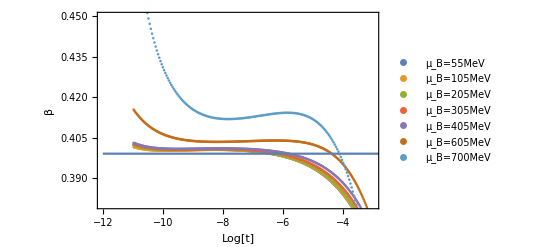

```mathematica
plotT=Show[ListPlot[{b1mub55,b1mub105,b1mub205,b1mub305,b1mub405,b1mub605,b1mub700},PlotRange->All,FrameLabel->{"Log[t]","β"},PlotLegends->{"μ_B=55MeV","μ_B=105MeV","μ_B=205MeV","μ_B=305MeV","μ_B=405MeV","μ_B=605MeV","μ_B=700MeV"}],ListLinePlot[{{-12,0.399},{1,0.399}}](*,PlotRange->All*),PlotRange->{{-12,-3},{0.38,0.45}},Frame->True]
```

```mathematica
Export["./tscaling.pdf",plotT]
```

./tscaling.pdf